```mathematica
(*Define symmetric quantization rho*)
CleanSlate;
$MinPrecision=MachinePrecision;
  ρz[z_] := z/(1 + Sqrt[1 - z])^2; 
 ρzb[z_] := ρz[Conjugate[z]]; 
 (*error estimates*)
    ρintErrorEstimateG[d_, DDs_, z_, γ_] := (2^(γ + 4*d)*β^(γ - 4*d)*Gamma[1 - γ + 4*d, β*DDs])/(Gamma[1 - γ + 4*d]*(1 - r^2)^γ)/.  {r -> Abs[ρz[z]], β -> -Log[Abs[ρz[z]]]}; 
      ρintErrorEstimateFt[d_, DDs_, z_, γ_] := 
     v^d*ρintErrorEstimateG[d, DDs, z, γ] + u^d*ρintErrorEstimateG[d, DDs, 1 - z, γ] /. {u -> z*Conjugate[z], v -> (1 - z)*(1 - Conjugate[z])}; 
     (*coefficients and prefactors*)
    kfunctAna[β_, x_] := Exp[(β/2)*Log[4*((1 - Sqrt[1 - x])^2/x)]]*(x/(2*(1 - x)^(1/4)*(1 - Sqrt[1 - x]))); 
    ConformalBlockAna[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunctAna[DD + l, z]*kfunctAna[DD - l - 2, Conjugate[z]] - 
       kfunctAna[DD + l, Conjugate[z]]*kfunctAna[DD - l - 2, z]);
       (*derivatives*)
       FAnaDer[DD_, l_, z_] := (1/(z - Conjugate[z]))*(-1)^(2*l)*(1 - z)*z*
      (1 - Conjugate[z])*Conjugate[z]*(-((2^(-5 + 2*DD)*((1 - Sqrt[z])/(1 + Sqrt[z]))^((1/2)*(-2*l + DD))*(1 - z)*
          ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^((1/2)*(-2*l + DD))*(-((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - 
           Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
           ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l) + (((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) + 
             Sqrt[z]*(((1 - Sqrt[z])/(1 + Sqrt[z]))^(2*l) - ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l)) + 
             ((1 - Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))^(2*l))*Sqrt[Conjugate[z]])*(1 - Conjugate[z])*
          (Log[16] + Log[-((-1 + Sqrt[z])/(1 + Sqrt[z]))] + Log[-((-1 + Sqrt[Conjugate[z]])/(1 + Sqrt[Conjugate[z]]))]))/
         ((-1 + Sqrt[z])^2*z^(1/4)*(-1 + Sqrt[Conjugate[z]])^2*Conjugate[z]^(1/4))) + (2^(-5 + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-2*l + DD))*z*
         ((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^((1/2)*(-2*l + DD))*Conjugate[z]*(-2*z*(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l)*
           (-1 + Sqrt[1 - Conjugate[z]]) + Conjugate[z]*(2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l) + 
            z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^(2*l) + (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^(2*l))))*
         (Log[16] + Log[(-1 + Sqrt[1 - z])^2/z] + Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*
         (-1 + Sqrt[1 - Conjugate[z]])^3*(1 - Conjugate[z])^(1/4))); 
	 ConformalBlockAnaDer[DD_, l_, z_] := 
     -((I*(-1)^l*2^(-6 - l + 2*DD)*((-1 + Sqrt[1 - z])^2/z)^((1/2)*(-l + DD))*Abs[z]^4*((-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z])^
         ((1/2)*(-l + DD))*(2*z*(-1 + Sqrt[1 - Conjugate[z]])*(-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l + 
         Conjugate[z]*(-2*(-1 + Sqrt[1 - z])*(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + z*(-(-((-2 + 2*Sqrt[1 - z] + z)/z))^l + 
             (-((-2 + 2*Sqrt[1 - Conjugate[z]] + Conjugate[z])/Conjugate[z]))^l)))*(Log[(16*(-1 + Sqrt[1 - z])^2)/z] + 
         Log[(-1 + Sqrt[1 - Conjugate[z]])^2/Conjugate[z]]))/((-1 + Sqrt[1 - z])^3*(1 - z)^(1/4)*(-1 + Sqrt[1 - Conjugate[z]])^3*
        (1 - Conjugate[z])^(1/4)*Im[z])); 
	kfunct[β_, x_] := kfunct[β, x] = x^(β/2)*Hypergeometric2F1[β/2, β/2, β, x]; 
    ConformalBlock[DD_, l_, z_] := ((-1)^l/2^l)*((z*Conjugate[z])/(z - Conjugate[z]))*(kfunct[DD + l, z]*kfunct[DD - l - 2, Conjugate[z]] - 
       kfunct[DD + l, Conjugate[z]]*kfunct[DD - l - 2, z]); 
      
      (*random sample of z around (1/2+I0)*)
           Sample[nz_,var_,seed_] := Module[{imax}, SeedRandom[seed];Table[Abs[RandomVariate[NormalDistribution[0, var]]]+
           1/2+I Abs[RandomVariate[NormalDistribution[0, var]]],{imax,1,nz}]]; 
qQGen[Δϕ_,Δ_,L_,zsample_]:=(((1 - zsample)*(1 - Conjugate[zsample]))^Δϕ    ConformalBlock[Δ, L , zsample]- ((zsample)*( Conjugate[zsample]))^Δϕ ConformalBlock[Δ, L,1- zsample])2^(L);qQGenDims[Δϕ_,ΔL_,z_]:=qQGen[1,#1[[1]],#1[[2]], z]&/@ΔL
```

```mathematica
(*Returns the square matrix of the coefficients*)
coefMat[Δϕ_,prec_, ΔL_]:=Block[{Nz,zsample,Idsample,errSample},
SetOptions[{RandomReal,RandomVariate},WorkingPrecision->prec];

$MinPrecision=prec;
$MaxPrecision=prec;

    SeedRandom[1323];
    Nz=Length[ΔL]+1;
  zsample = Sample[Nz,1/100,1232]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
errSample= ρintErrorEstimateFt[1,ΔL[[-1,1]],#,1]&/@zsample//Flatten;
Return[Transpose[Join[qQGenDims[Δϕ,ΔL,zsample], {Idsample}]]/errSample]];
```

```mathematica
lmax=20;
ΔL={#+2,#}&/@Range[0,lmax,2]
eigenvecs=Table[coefMat[1,50, ΔL[[1;;i]]]//Eigenvalues//Abs//Log,{i,2,lmax/2+1}];
```

{{2,0},{4,2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14},{18,16},{20,18},{22,20}}

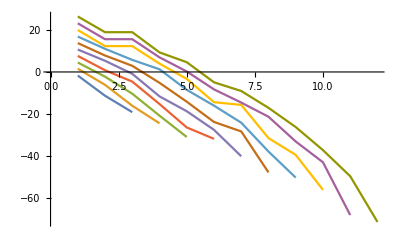

```mathematica
ListPlot[eigenvecs,Joined->True]
```

```mathematica
absolutedMatrix=Table[coefMat[1,50, ΔL[[1;;i]]]//Abs//Log,{i,2,lmax/2+1}];
```

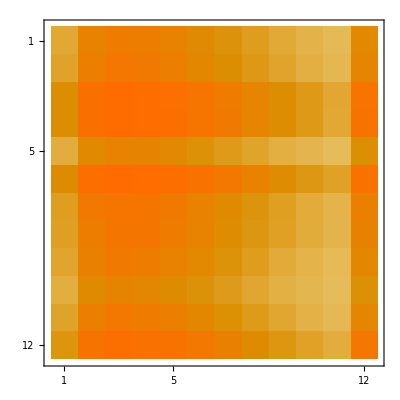

```mathematica
MatrixPlot[absolutedMatrix[[10]]](*Top line Identity, successive operators downwards*)
```

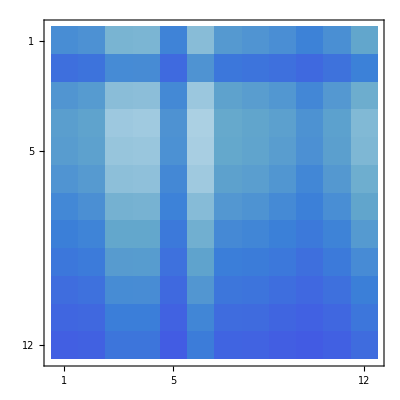

```mathematica
absolutedMatrixAverageValues=Table[coefMat[1,50, ΔL[[1;;i]]]//Abs//Log//Mean,{i,2,lmax/2+1}];
```

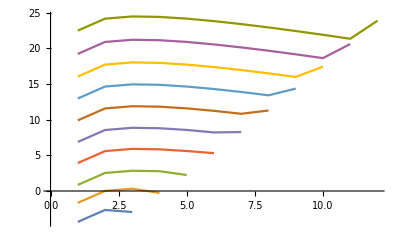

{{2,0},{4,2}}

```mathematica
ListPlot[absolutedMatrixAverageValues,Joined->True]
```

```mathematica
coefMat2dPlot[Δϕ_,prec_, ΔL_]:=Block[{Nz},
SetOptions[{RandomReal,RandomVariate},WorkingPrecision->prec];

$MinPrecision=prec;
$MaxPrecision=prec;

    SeedRandom[1323];
    Nz=Length[ΔL]+1;
  zsample = Sample[Nz,1/100,1232]; 
Idsample = SetPrecision[Table[(zsample[[zv]]*Conjugate[zsample[[zv]]])^Δϕ -
        ((1 - zsample[[zv]])*(1 - Conjugate[zsample[[zv]]]))^Δϕ, {zv, 1, Nz}],prec];
Export["plot_eig_1"<>ToString[prec]<>".pdf",ContourPlot[(Join[ {Idsample},qQGenDims[Δϕ,{{SetPrecision[2+x,prec],0},{SetPrecision[4+y,prec],2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14}},zsample]]//Eigenvalues//Abs//Log)[[1]],{x,-0.1,0.1},{y,-0.1,0.1}]];
Export["plot_eig_2"<>ToString[prec]<>".pdf",ContourPlot[(Join[ {Idsample},qQGenDims[Δϕ,{{SetPrecision[2+x,prec],0},{SetPrecision[4+y,prec],2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14}},zsample]]//Eigenvalues//Abs//Log)[[2]],{x,-0.1,0.1},{y,-0.1,0.1}]];
Export["plot_det_"<>ToString[prec]<>".pdf",ContourPlot[(Join[ {Idsample},qQGenDims[Δϕ,{{SetPrecision[2+x,prec],0},{SetPrecision[4+y,prec],2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14}},zsample]]//Det),{x,-0.1,0.1},{y,-0.1,0.1}]];
]
```

```mathematica
coefMat2dPlot[1,80,{{2,0},{4,2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14}}]
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

$Aborted

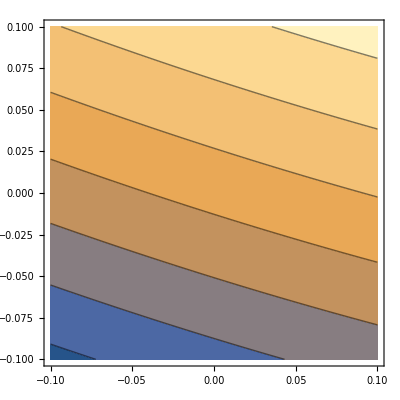

```mathematica
ContourPlot[(coefMat[1,50,{{SetPrecision[2+x,50],0},{SetPrecision[4+y,50],2}}]//Eigenvalues//Abs//Log)[[2]],{x,-0.1,0.1},{y,-0.1,0.1}]
```

```mathematica
coefMat[1,50,{{SetPrecision[2+x,50],0},{40/10,2},{6,4},{8,6},{10,8},{12,10},{14,12},{16,14},{18,16},{20,18},{22,20}}]//Eigenvalues//Abs//Log
```